## System Potential of continuous logistic w/ Allee effect

```mathematica
Clear["Global`*"]
```

```mathematica
dNdt=r Ν (1-Ν/K)(Ν/A-1)
```

r Ν (-1+Ν/A) (1-Ν/K)

```mathematica
parms={r->1,K->10,A->5};
```

```mathematica
dNdt/.parms
```

(1-Ν/10) (-1+Ν/5) Ν

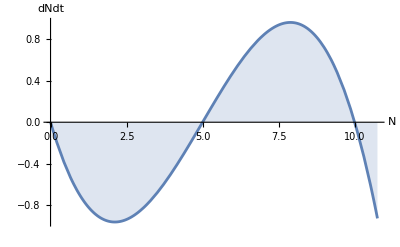

```mathematica
p1=Plot[dNdt/.parms,{Ν,0,10.75},
Filling->Axis,
AxesLabel->{"N","dNdt"}
]
```

```mathematica
equil=Solve[dNdt==0,Ν];
%//TableForm
```

Ν→0
Ν→A
Ν→K

#### Derivative of dN/dt w.r.t. N

```mathematica
fDeriv=D[dNdt,Ν]//Expand
```

-r+(2 r Ν)/A+(2 r Ν)/K-(3 r Ν^2)/(A K)

#### Evaluate first derivative at each equilibrium

```mathematica
fDeriv=fDeriv/.equil//Simplify;
TableForm[{{equil,fDeriv,fDeriv/.parms}}]
```

Ν→0
Ν→A
Ν→K | -r
r-(A r)/K
r-(K r)/A | -1
1/2
-1

```mathematica
System Potential
```

```mathematica
pN=-Integrate[dNdt,Ν]//Expand
```

```mathematica
pN=-∫dNdtⅆΝ//Expand
```

```mathematica
p2=Plot[pN/.parms,{Ν,0,12},
Filling->Axis,
AxesLabel->{"N","ϕ"}];
GraphicsGrid[{{p1},{p2}}]
```